Set::nosym: _ does not contain a symbol to attach a rule to.

General::stop: Further output of Set::nosym will be suppressed during this calculation.

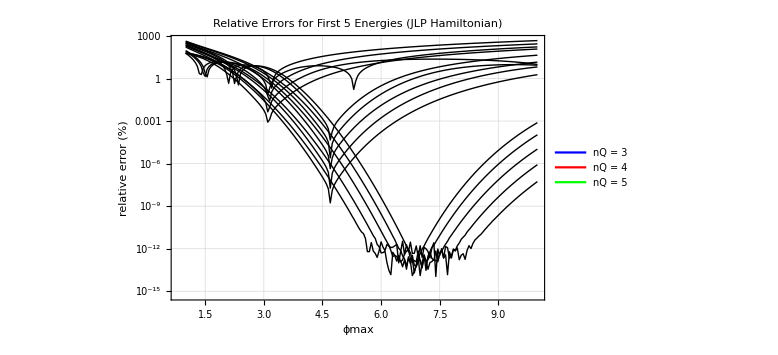

```mathematica
Hamiltonian[ns_, phiMax_]:= Module [
{deltaPhi, beta, phi, phi2, kmax, deltaK,betak, k, F, Pik2, Piphi2, H},

(*each of the phi and pi matricies (position and momentum equivalents) and diagonal in their own space, we apply the QuFoTr to the matricies to move back and forth *)

deltaPhi = 2 phiMax/(ns-1);
beta = Range[0, ns-1];
phi = -phiMax + beta deltaPhi;

phi2 = DiagonalMatrix[phi^2]; (*diagonal phi squared matrix in the field space*)

kmax = Pi/deltaPhi;
deltaK = 2 Pi/ (deltaPhi ns);
betak = Range[1, ns];
k = -kmax + betak deltaK;

F = Exp[-I Outer[Times, k, phi]]/Sqrt[ns]; (*creates a unitary Fourier matrix that transforms between the field basis and the momentum basis F phi = K*)

Pik2 = DiagonalMatrix[k^2];(*diagonal pi squared matrix in momentum space*)

Piphi2 = ConjugateTranspose[F]. Pik2.F; (*pi squared matrix in field space*)

H = 0.5 (phi2 + Piphi2) (*Hamiltonian*)
(*might end up being slightly none hermitian because computers so:*);
H= 0.5 (H + ConjugateTranspose[H]);

{H,phi}
];

FindPrecision[ns_, phiMax_] := Module[
{H, ordereig, eiglow, eigexact, relerror},

{H, _} = Hamiltonian[ns, phiMax]; (*grabbing value of the hamiltonian from ^ function*)
ordereig = Sort[Re[Eigenvalues[H]]];
eiglow = ordereig[[1 ;; Min[5, Length[ordereig]]]]; (*gets five lowest eigenvalues of hamiltonian like in savage*)
eigexact = Range[0,4] +0.5 ;(*gets exact HO energies*)
relerror = Abs[(eiglow-eigexact)/eigexact]*100;
relerror
];

nqList={3,4,5};
phiMaxValues=Range[1,10,0.05];
results=Association[]; (*basically a python dictionary*)

Do[ns=2^nq;
results[nq]=Table[{phiMax,FindPrecision[ns,phiMax]},{phiMax,phiMaxValues}];,(*calls find preciscion for each phimax and ns and makes a table of them*)
{nq,nqList}
]; (*loops over each nq in nqlist*)

plotGroups=Table[Table[Table[ (*still dont really get why I had to do table 3 times*)
{results[nq][[i,1]],results[nq][[i,2,j]]},{i,Length[results[nq]]}],
{j,5}],
{nq,nqList} (*loops over each nq in the nq list for each of the errors in each energy level*)
];

colorList={Blue,Red,Green}; (*colours*)

allCurves=Flatten[Table[Table[Style[Table[ (*know why I need flatten and style but why I need three table things is beyond me*)
{results[nqList[[m]]][[i,1]],results[nqList[[m]]][[i,2,j]]},{i,Length[results[nqList[[m]]]]}], (*m loops over the nq indicies*)
colorList[[m]],Thick],{j,5}], (*j loops over the eenrgy levels*)
{m,Length[nqList]}],1 (*again iteration stuff*)
];

legendLabels=Table["nQ = "<>ToString[nqList[[m]]],{m,Length[nqList]}]; (*makes the legend labels*)

ListLogPlot[allCurves, (*plots as log log graph and which data to plot*) 
Joined->True,(*should the data be connected with lines*)
Frame->True, (*Full Frame instead of standard axis*)
FrameLabel->{"ϕmax","relative error (%)"}, (*axis labels*)
PlotLegends->Placed[LineLegend[colorList,legendLabels,LegendMarkerSize->30],Below], (*adds legend with labels and size and colour*)
GridLines->Automatic,(*Background gridlines*)
PlotLabel->Style["Relative Errors for First 5 Energies (JLP Hamiltonian)",16], (*title*)
ImageSize->Large,
PlotRange->All] (*makes sure all of the data is included*)
```